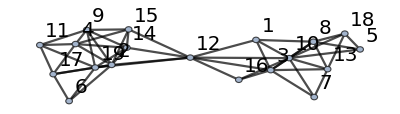

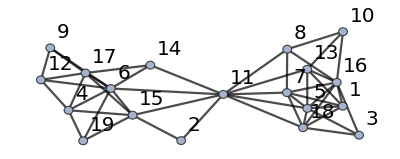

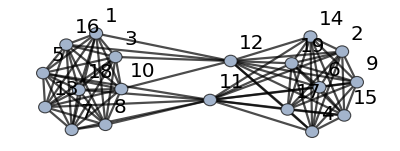

```mathematica
G1=System`Graph[{1<->3,1<->8,1<->10,1<->12,2<->4,2<->6,2<->9,2<->12,2<->14,2<->15,2<->17,2<->19,3<->7,3<->8,3<->10,3<->12,3<->13,3<->16,4<->9,4<->11,4<->14,4<->15,4<->17,5<->8,5<->10,5<->18,6<->17,6<->19,7<->10,7<->13,8<->10,8<->13,8<->18,9<->11,9<->14,9<->15,9<->19,10<->12,10<->13,10<->16,10<->18,11<->17,11<->19,12<->14,12<->15,12<->16,12<->19,13<->18,14<->15,14<->19,17<->19},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
G2=System`Graph[{1<->5,1<->7,1<->13,1<->16,1<->18,2<->11,2<->15,3<->5,3<->16,3<->18,4<->6,4<->12,4<->15,4<->17,4<->19,5<->7,5<->11,5<->13,5<->16,5<->18,6<->9,6<->11,6<->12,6<->14,6<->15,6<->17,6<->19,7<->8,7<->11,7<->16,7<->18,8<->10,8<->11,8<->16,9<->12,9<->17,10<->13,10<->16,11<->13,11<->14,11<->15,11<->18,12<->17,13<->16,14<->17,15<->17,15<->19,16<->18},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNION=GraphUnion[G1,G2,VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]
GUNIONComplement=GraphComplement[GUNION,VertexLabels->"Name",VertexSize->0.1,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}];
```

```mathematica
<<Combinatorica`
<<GraphUtilities`
BrelazColoringList[G_]:=(brelazz=BrelazColoring@ToCombinatoricaGraph[G];Print[Table[{i,Part[brelazz,i]},{i,Length[brelazz]}]//TableForm];Return[brelazz]);
BrelazChromatic[G_]:=Max[BrelazColoring@ToCombinatoricaGraph[G]];
MVCColoringList[G_]:=(mvc=MinimumVertexColoring@ToCombinatoricaGraph[G];Print[Table[{i,Part[mvc,i]},{i,Length[mvc]}]//TableForm];Return[mvc]);
GetChromaticNumber[G_]:=Return[Max[MinimumVertexColoring@ToCombinatoricaGraph[G]]];
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
GUNIONCR=Ceiling[VertexCount[GUNION]/2];
GPruned=GUNION;
i=1;
Parallelize[While[i≤ VertexCount[GUNION],If[GetChromaticNumber[VertexDelete[GPruned,i]]≥ GUNIONCR,GPruned=VertexDelete[GPruned,i];Print[i,": DELETED " ],Print[i]];i++];]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

```mathematica
GUNIONEdgeList=EdgeList[GPruned];
GUNIONEdgeListCnt=EdgeCount[GPruned];
i=1;
Parallelize[While[i≤ GUNIONEdgeListCnt,If[GetChromaticNumber[EdgeDelete[GPruned,GUNIONEdgeList[[i]]]]≥ GUNIONCR,GPruned=EdgeDelete[GPruned,GUNIONEdgeList[[i]]];Print[GUNIONEdgeList[[i]],": DELETED " ],Print[GUNIONEdgeList[[i]]]];i++];]
```

1<->2

1<->3

1<->4

1<->6

1<->8

1<->11

1<->12

1<->14

1<->15

1<->17

2<->3

2<->4

2<->6

$Aborted

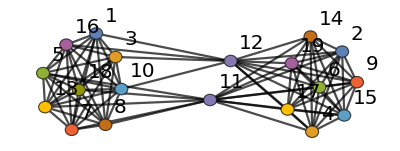

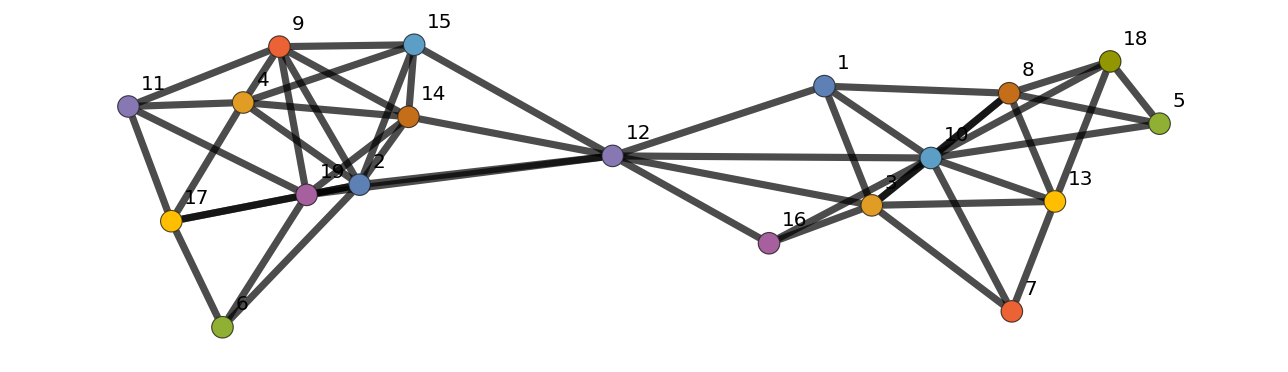

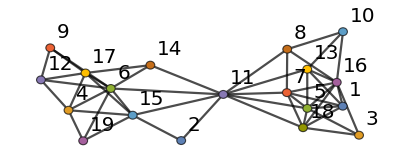

```mathematica
mvc={1,1,2,2,3,3,4,6,4,7,5,5,8,6,7,9,8,10,9};
GUNIONCOLORED=SetProperty[GUNION,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G1=SetProperty[G1,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
G2=SetProperty[G2,System`VertexStyle->Thread[System`VertexList[GUNION]->(ColorData[97]/@mvc)]]
Export["1.eps",G1];
Export["2.eps",G2];
```

1  42

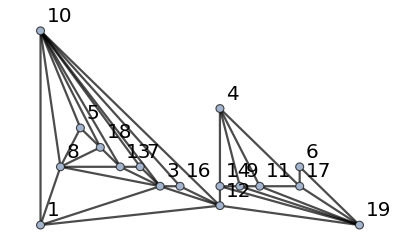
2 -Graphics- 39

3  39

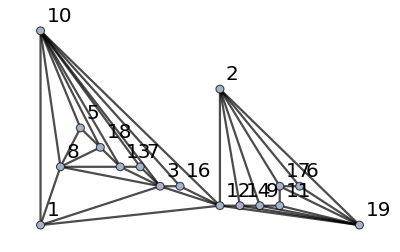
4 -Graphics- 41

5  43

6  43

7  43

8  40

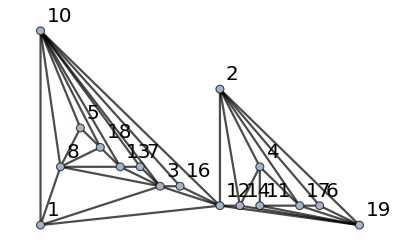
9 -Graphics- 41

10  37

11  42

12  39

13  41

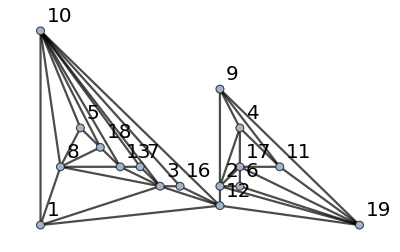
14 -Graphics- 41

VertexDelete::inv: The argument {15,15} in VertexDelete[Graph[<19>, <51>], {15, 15}] is not a valid vertex.

SetProperty::pvobj: … is not an object with properties.

EdgeCount::graph: A graph object is expected at position 1 in ….

15 SetProperty[VertexDelete[-Graphics-,{15,15}],GraphLayout→PlanarEmbedding] EdgeCount[SetProperty[VertexDelete[-Graphics-,{15,15}],GraphLayout→PlanarEmbedding]]

16  43

17  41

18  42

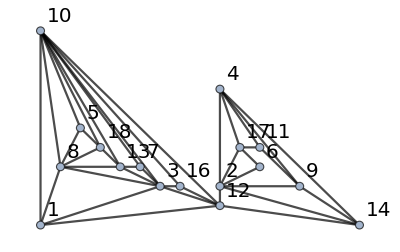
19 -Graphics- 39

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[A=SetProperty[VertexDelete[G1,{i,15}],GraphLayout->"PlanarEmbedding"];Print[i," ",A," ", EdgeCount[A]],{i,1,19}]
```

```mathematica
Table[PropertyValue[{MyDraw,n},VertexCoordinates],{n,1,19}]
EdgeList[MyDraw]
```

{{0.,0.},{9.,2.},{6.,2.},{10.,5.},{2.,5.},{10.,2.},{5.,3.},{1.,3.},{9.,7.},{0.,10.},{12.,3.},{9.,1.},{4.,3.},$Failed,$Failed,{7.,2.},{10.,3.},{3.,4.},{16.,0.}}

{1<->3,1<->8,1<->10,1<->12,2<->4,2<->6,2<->9,2<->12,2<->17,2<->19,3<->7,3<->8,3<->10,3<->12,3<->13,3<->16,4<->9,4<->11,4<->17,5<->8,5<->10,5<->18,6<->17,6<->19,7<->10,7<->13,8<->10,8<->13,8<->18,9<->11,9<->19,10<->12,10<->13,10<->16,10<->18,11<->17,11<->19,12<->16,12<->19,13<->18,17<->19}

1  39

2  41

3  40

4  38

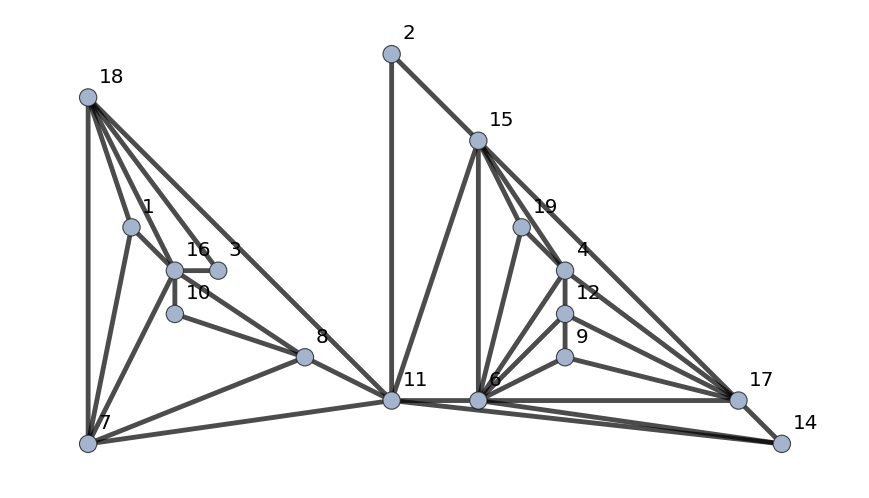
5 -Graphics- 37

6  35

7  37

8  39

9  40

10  41

11  35

12  39

VertexDelete::inv: The argument {13,13} in VertexDelete[Graph[<19>, <48>], {13, 13}] is not a valid vertex.

SetProperty::pvobj: … is not an object with properties.

EdgeCount::graph: A graph object is expected at position 1 in ….

13 SetProperty[VertexDelete[-Graphics-,{13,13}],GraphLayout→PlanarEmbedding] EdgeCount[SetProperty[VertexDelete[-Graphics-,{13,13}],GraphLayout→PlanarEmbedding]]

14  40

15  37

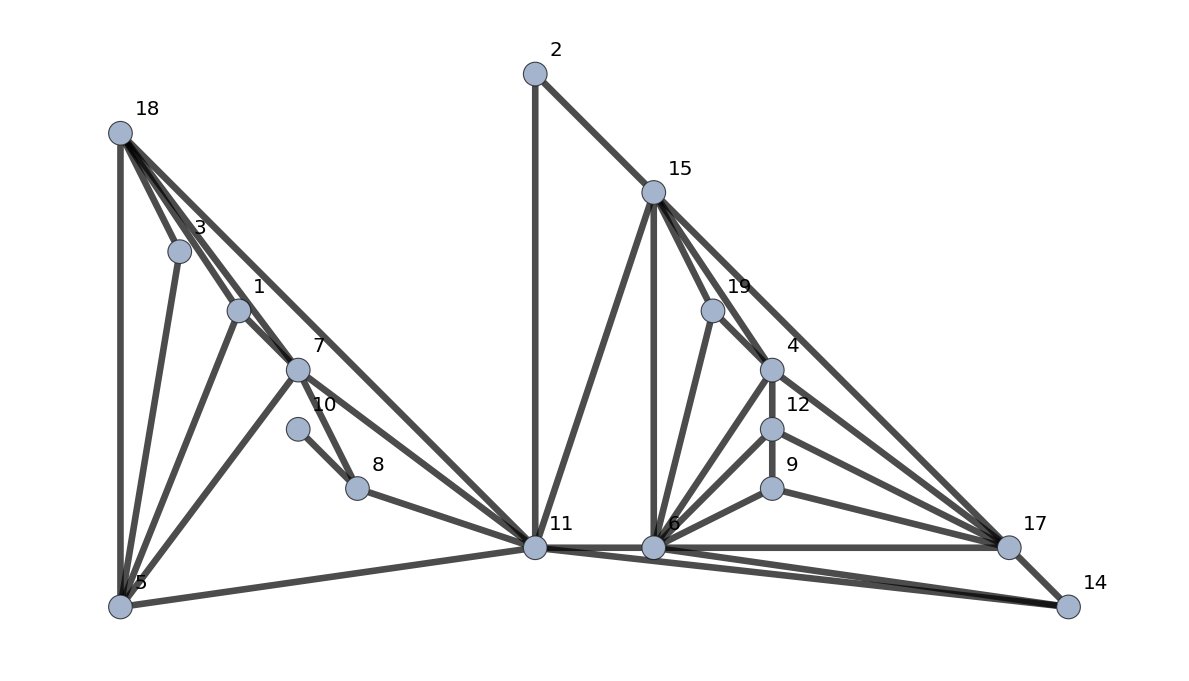
16 -Graphics- 36

17  37

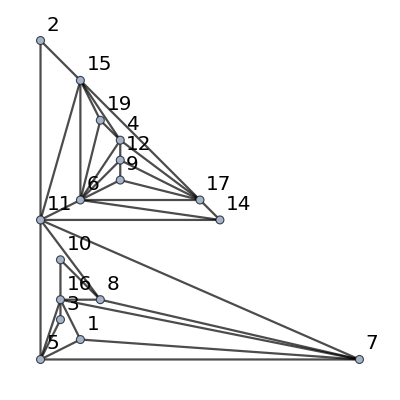
18 -Graphics- 37

19  40

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[A=SetProperty[VertexDelete[G2,{i,13}],GraphLayout->"PlanarEmbedding"];Print[i," ",A," ", EdgeCount[A]],{i,1,19}]
```